```mathematica
SetOptions[EvaluationNotebook[],CellEpilog:>SelectionMove[EvaluationNotebook[],Next,Cell]]
```

Variables used in model

```mathematica
(* variables and parameters at (homogeneous) steady state *)
ssvars = { ξ-> 0.1, koff->0.1, kon-> 1, Dμ->1, Dc-> 10, β->1000, α->1000 ,kd->  0.1 ,R-> 10, μ0->10000, Pe-> 2500, ζ-> -Pe*ξ*((Dc*koff + Dμ*kon)/kon)/μ0};
startc = koff*μ0/kon//.ssvars;
startμ = μ0//.ssvars;
kappa=0.01;
Tend = 150;
```

solver for 1D cell

```mathematica
pdeSolve[rdvariables_] :=Module[{sol},
sol = NDSolve[{
D[δρ[θ, t], t]+(1/R)*D[((1+δρ[θ, t]) *v[θ, t]), θ]== -kd*δρ[θ, t],
D[(-ζ*μ[θ, t] -α*δρ[θ, t] + (β/R^2)*D[δρ[θ, t], θ,θ]), θ] ==ξ *R *v[θ, t],
D[c[θ, t], t]== (Dc/R^2)* D[c[θ, t], θ,θ]-kon*c[θ, t]+koff*μ[θ, t],
D[μ[θ, t], t]+(1/R)* D[(μ[θ, t]*v[θ, t]), θ]== kon*c[θ, t]-koff*μ[θ, t] + (Dμ/R^2)*D[μ[θ,t], θ,θ],

c[θ, 0]== startc + kappa*Cos[θ-Pi] ,
μ[θ, 0] ==  startμ + kappa*Cos[θ-Pi] ,
δρ[θ,0]==kappa*Cos[θ-Pi],
v[θ,0] == kappa*Sin[θ],

μ[-Pi, t]==μ[Pi, t],
c[-Pi, t]==c[Pi, t],
δρ[-Pi, t]==δρ[Pi, t],
v[-Pi,t]==v[Pi,t]
}//.rdvariables,{μ, c, δρ, v},{θ,-Pi,Pi},{t, 0,Tend}, MaxStepFraction->1/100,Method->Automatic]; Return[sol]]
```

```mathematica
(* alternatively can try Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->nx,"MaxPoints"->nx},Method->{"IDA","ImplicitSolver"->{"GMRES"}}} *)
```

```mathematica
(* set up some functions for plotting *)
plotSolVel[tMin_,tMax_,plInt_,soln_]:=Quiet[Table[Labeled[Plot[Evaluate[v[θ, t]/.soln/.t->i//.ssvars],{θ,-Pi,Pi},PlotStyle->RGBColor[0.61,0.79,0.47], PlotRange->All,PlotLegends->{"vel"}]," t:"<>ToString@i],{i,tMin,tMax,plInt}]]
plotSolrhoMu[tMin_,tMax_,plInt_,soln_]:=Quiet[
Table[Labeled[Plot[Evaluate[{δρ[θ,t], μ[θ,t]*0.0001}/.soln/.t->i],{θ,-Pi,Pi},PlotRange->All,PlotStyle->{RGBColor[0.84,0.28,0.62],RGBColor[0.96,0.7,0.3]}, PlotLegends->{"δρ", "μ(10^4)"}]," t:"<>ToString@i],{i,tMin,tMax,plInt}]]
plotSolc[tMin_,tMax_,plInt_,soln_]:=Quiet[
Table[Labeled[Plot[c[θ,t]/.soln/.t->i,{θ,-Pi,Pi},PlotStyle-> RGBColor[0.32,0.67,0.78], PlotRange->All, PlotLegends->{"c"}]," t:"<>ToString@i],{i,tMin,tMax,plInt}]]
```

```mathematica
(* now solve from steady state + small perturbation to check for pattern-formation instability. Ignore stability warnings, an instability is what we are looking for in pattern formation *)
solss = pdeSolve[ssvars]
```

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

NDSolve::eerr: Warning: scaled local spatial error estimate of 1055.62 at t = 150. in the direction of independent variable θ is much greater than the prescribed error tolerance. Grid spacing with 101 points may be too large to achieve the desired accuracy or precision. A singularity may have formed or a smaller grid spacing can be specified using the MaxStepSize or MinPoints method options.

{{μ→InterpolatingFunction[{{…, -3.14159, 3.14159, …}, {0., 150.}}, <>],c→InterpolatingFunction[{{…, -3.14159, 3.14159, …}, {0., 150.}}, <>],δρ→InterpolatingFunction[{{…, -3.14159, 3.14159, …}, {0., 150.}}, <>],v→InterpolatingFunction[{{…, -3.14159, 3.14159, …}, {0., 150.}}, <>]}}

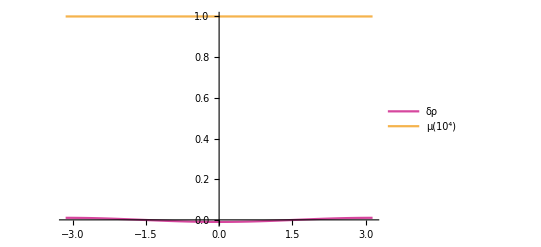
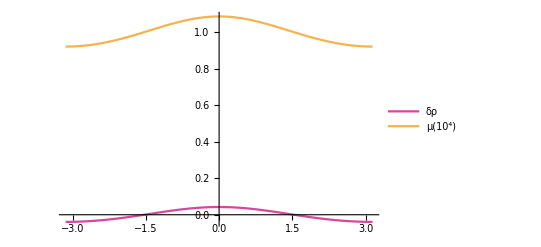
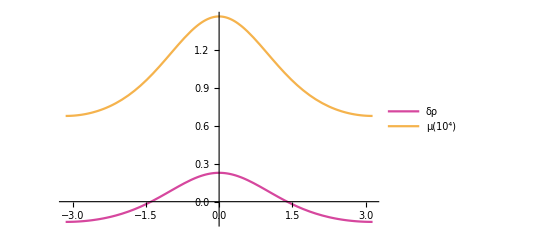
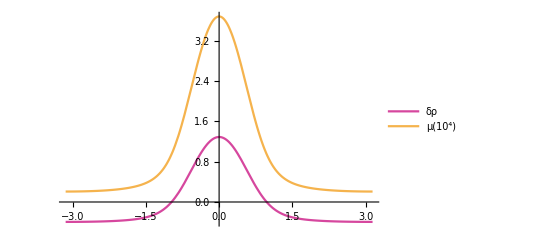
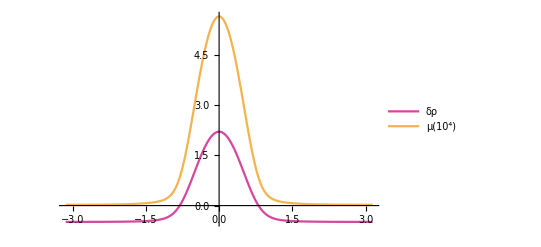
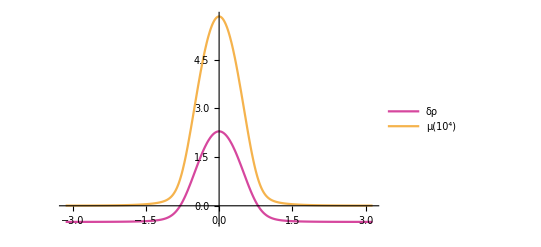
{-Graphics- t:0,-Graphics- t:30,-Graphics- t:60,-Graphics- t:90,-Graphics- t:120,-Graphics- t:150}

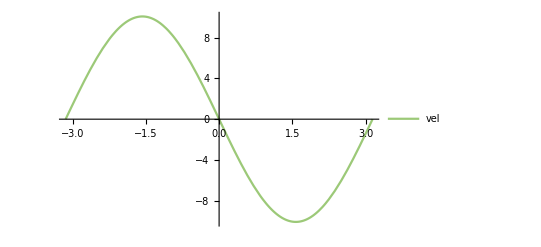
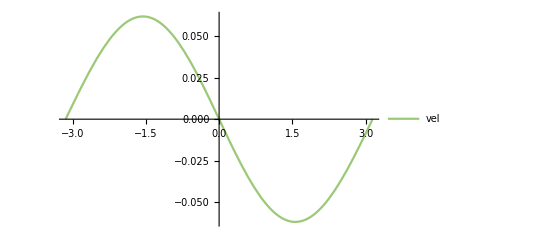
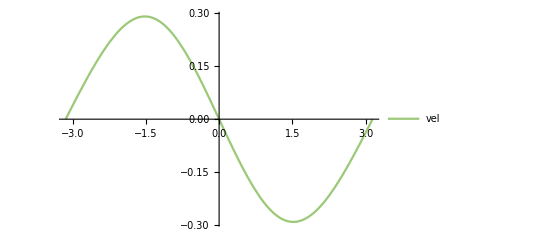
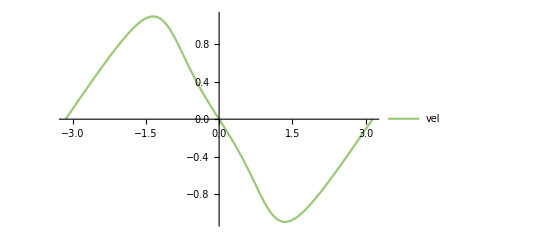
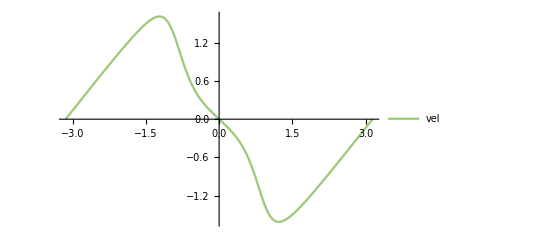
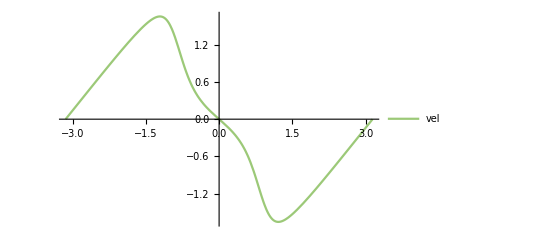
{-Graphics- t:0,-Graphics- t:30,-Graphics- t:60,-Graphics- t:90,-Graphics- t:120,-Graphics- t:150}

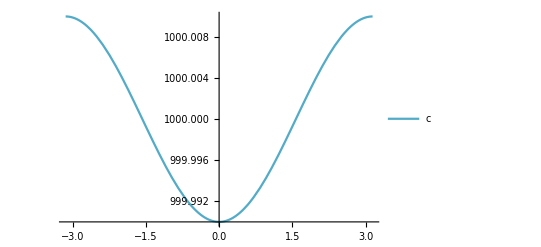
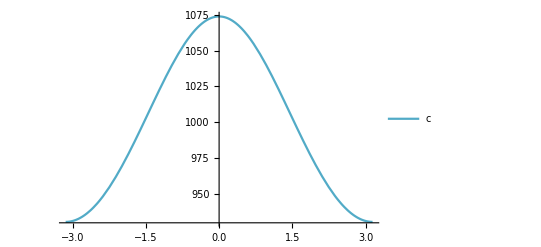
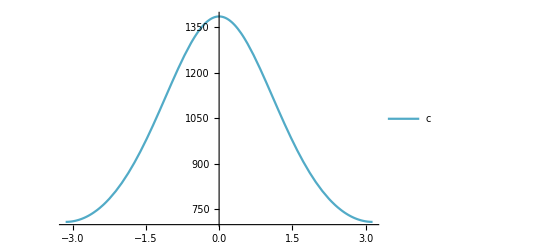
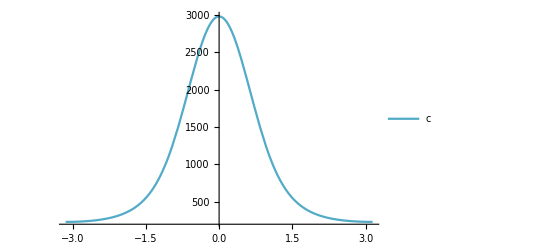
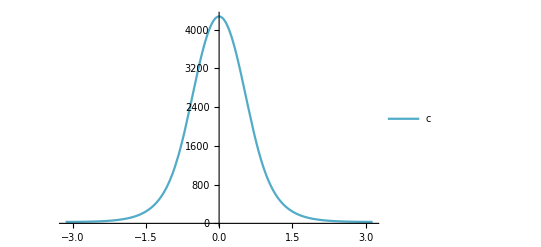
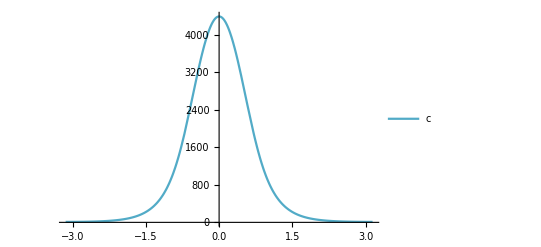
{-Graphics- t:0,-Graphics- t:30,-Graphics- t:60,-Graphics- t:90,-Graphics- t:120,-Graphics- t:150}

```mathematica
rhomuplot = plotSolrhoMu[0,Tend,Tend/5,solss]
velplot = plotSolVel[0,Tend,Tend/5,solss]
cplot = plotSolc[0,Tend,Tend/5,solss]
```

```mathematica
(* extract steady state to continue solution with perturbation*)
csol= c/.solss[[1]];
μsol = μ/.solss[[1]];
δρsol = δρ/.solss[[1]];
vsol = v/.solss[[1]];
```

```mathematica
css=Interpolation[Transpose[Append[{csol["Coordinates"][[1]]},csol["ValuesOnGrid"][[All,-1]]]],InterpolationOrder->csol["InterpolationOrder"][[1]],Method->csol["InterpolationMethod"],PeriodicInterpolation->True];
μss=Interpolation[Transpose[Append[{μsol["Coordinates"][[1]]},μsol["ValuesOnGrid"][[All,-1]]]],InterpolationOrder->μsol["InterpolationOrder"][[1]],Method->μsol["InterpolationMethod"],PeriodicInterpolation->True];
δρss=Interpolation[Transpose[Append[{δρsol["Coordinates"][[1]]},δρsol["ValuesOnGrid"][[All,-1]]]],InterpolationOrder->δρsol["InterpolationOrder"][[1]],Method->δρsol["InterpolationMethod"],PeriodicInterpolation->True];
vss=Interpolation[Transpose[Append[{vsol["Coordinates"][[1]]},vsol["ValuesOnGrid"][[All,-1]]]],InterpolationOrder->vsol["InterpolationOrder"][[1]],Method->vsol["InterpolationMethod"],PeriodicInterpolation->True];
(* see stack exchange post https://mathematica.stackexchange.com/questions/110377/extract-one-dimension-from-an-n-dimensional-interpolatingfunction?rq=1 *)
```

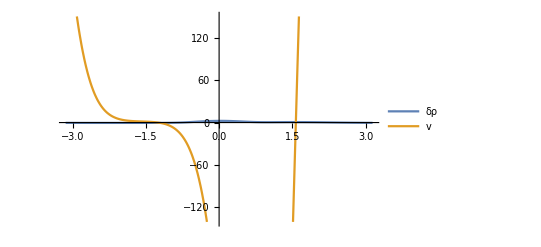

```mathematica
(* set and plot perturbation*)
Tplus = 20;
θp = Pi*4/8;
sp = 0.5;

(*apply perturbations*)
δρp[θ_,θpp_,spp_]:= spp*δρss[0]*(Exp[-(θ-θpp)^2] + Exp[-(θ-(θpp + 2Pi))^2]+ Exp[-(θ-(θpp - 2Pi))^2])
δρpp0[θ_,θpp_,spp_] := δρss[θ]+δρp[θ,θpp,spp]
vp[θ_,θpp_,spp_]= D[(-α*δρp[θ,θpp,spp] + (β/R^2)*D[δρp[θ,θpp,spp], θ,θ]), θ]/ξ /R //.ssvars;
vpp0[θ_,θpp_,spp_]=vss[θ] + vp[θ,θpp,spp];
(*use = instead of := to not delay evaluation of derivative*)
Plot[{δρpp0[θ,θp,sp],vpp0[θ,θp,sp]},{θ,-Pi,Pi},PlotLegends->{"δρ","v"}]
```

```mathematica
(* now solve the PDE again with initial conditions at steady state, plus a perturbation *)
pdeSolvePerturb[rdvariables_,θpp_,spp_] :=Module[{sol},
sol = NDSolve[{
D[δρ[θ, t], t]+(1/R)*D[((1+δρ[θ, t]) *v[θ, t]), θ]== -kd*δρ[θ, t],
D[(-ζ*μ[θ, t] -α*δρ[θ, t] + (β/R^2)*D[δρ[θ, t], θ,θ]), θ] ==ξ *R *v[θ, t],
D[c[θ, t], t]== (Dc/R^2)* D[c[θ, t], θ,θ]-kon*c[θ, t]+koff*μ[θ, t],
D[μ[θ, t], t]+(1/R)* D[(μ[θ, t]*v[θ, t]), θ]== kon*c[θ, t]-koff*μ[θ, t] + (Dμ/R^2)*D[μ[θ,t], θ,θ],

c[θ, 0]== css[θ],
μ[θ, 0] ==μss[θ],
δρ[θ,0]==δρpp0[θ,θpp,spp],
v[θ,0] == vpp0[θ,θpp, spp],

μ[-Pi, t]==μ[Pi, t],
c[-Pi, t]==c[Pi, t],
δρ[-Pi, t]==δρ[Pi, t],
v[-Pi,t]==v[Pi,t]
}//.rdvariables,{μ, c, δρ, v},{θ,-Pi,Pi},{t, 0,Tplus}, MaxStepFraction->1/100,Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MaxPoints"->200}}]; Return[sol]]
```

```mathematica
solpp = pdeSolvePerturb[ssvars,θp,sp]
```

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

NDSolve::mxsst: Using maximum number of grid points 200 allowed by the MaxPoints or MinStepSize options for independent variable θ.

NDSolve::eerr: Warning: scaled local spatial error estimate of 55.983 at t = 20. in the direction of independent variable θ is much greater than the prescribed error tolerance. Grid spacing with 201 points may be too large to achieve the desired accuracy or precision. A singularity may have formed or a smaller grid spacing can be specified using the MaxStepSize or MinPoints method options.

{{μ→InterpolatingFunction[{{…, -3.14159, 3.14159, …}, {0., 20.}}, <>],c→InterpolatingFunction[{{…, -3.14159, 3.14159, …}, {0., 20.}}, <>],δρ→InterpolatingFunction[{{…, -3.14159, 3.14159, …}, {0., 20.}}, <>],v→InterpolatingFunction[{{…, -3.14159, 3.14159, …}, {0., 20.}}, <>]}}

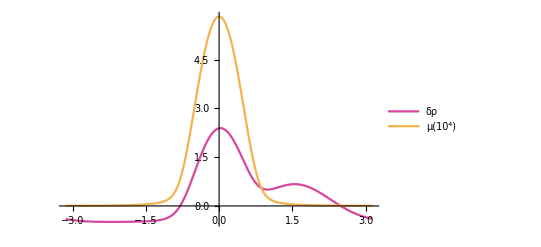
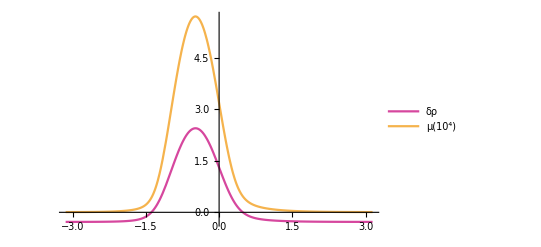
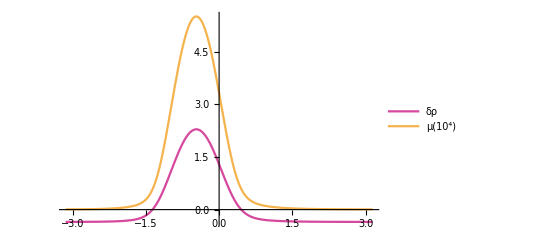
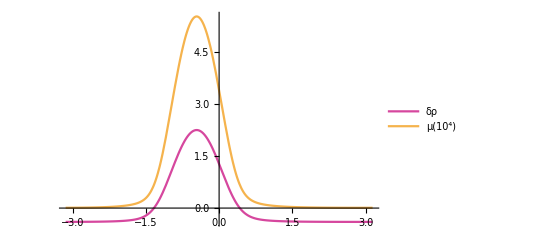
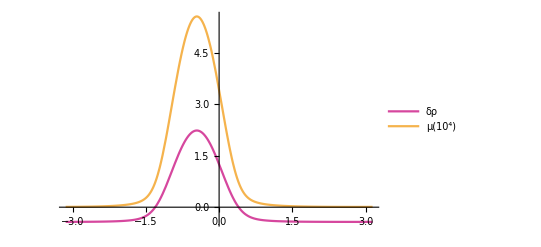
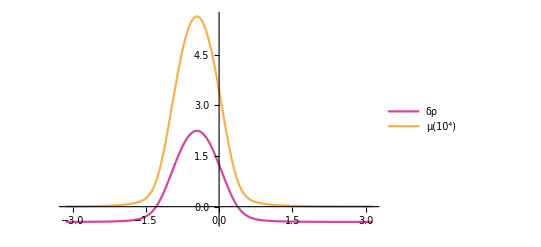
{-Graphics- t:0,-Graphics- t:4,-Graphics- t:8,-Graphics- t:12,-Graphics- t:16,-Graphics- t:20}

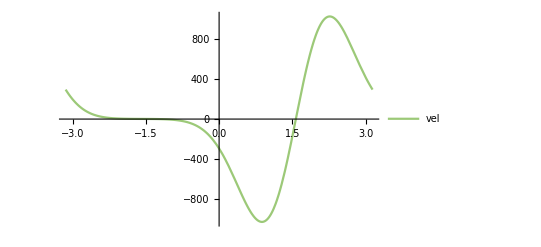
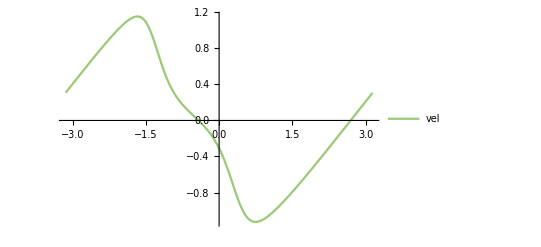
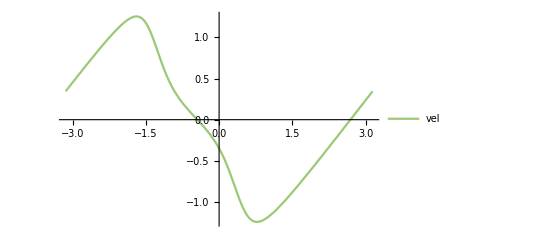
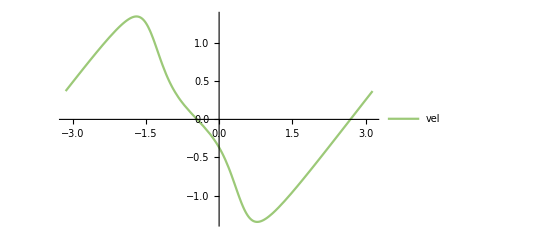
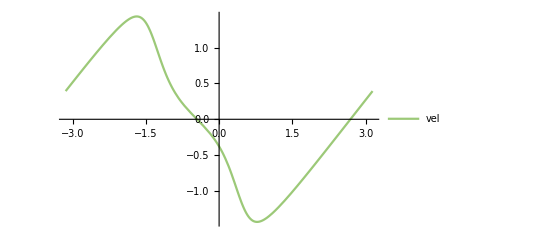
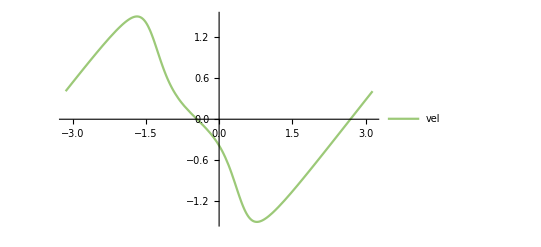
{-Graphics- t:0,-Graphics- t:4,-Graphics- t:8,-Graphics- t:12,-Graphics- t:16,-Graphics- t:20}

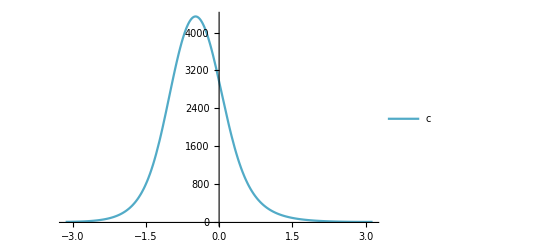
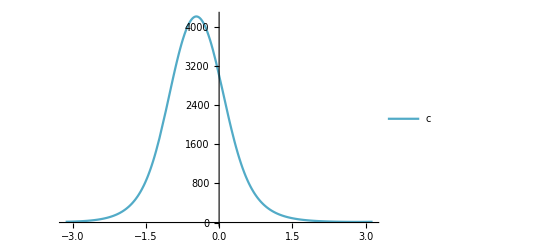
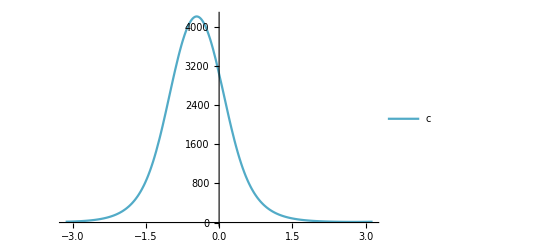
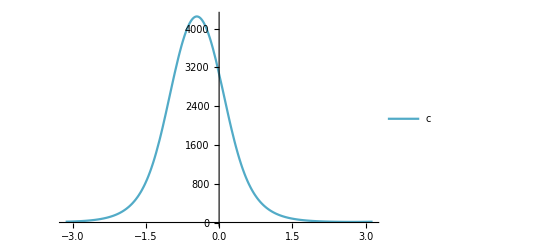
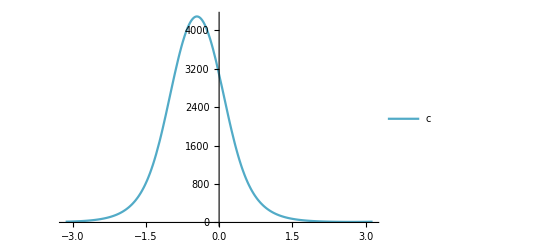
{-Graphics- t:0,-Graphics- t:4,-Graphics- t:8,-Graphics- t:12,-Graphics- t:16,-Graphics- t:20}

```mathematica
rhomuplotpp = plotSolrhoMu[0,Tplus,Tplus/5,solpp]
velplotpp = plotSolVel[0,Tplus,Tplus/5,solpp]
cplotpp = plotSolc[0,Tplus,Tplus/5,solpp]
```

```mathematica
θf = θ/.Last[FindMaximum[{Flatten[μ/.solpp[[1]] ][θ,Tplus]},{{θ,0}}]]
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

-0.125186

```mathematica
θfinal[θpp_,spp_] := θ/.Last[FindMaximum[{Flatten[μ/.pdeSolvePerturb[ssvars,θpp,spp][[1]] ][θ,Tplus]},{{θ,0}}]]
```

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

NDSolve::mxsst: Using maximum number of grid points 200 allowed by the MaxPoints or MinStepSize options for independent variable θ.

NDSolve::eerr: Warning: scaled local spatial error estimate of 46.7716 at t = 20. in the direction of independent variable θ is much greater than the prescribed error tolerance. Grid spacing with 201 points may be too large to achieve the desired accuracy or precision. A singularity may have formed or a smaller grid spacing can be specified using the MaxStepSize or MinPoints method options.

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

NDSolve::mxsst: Using maximum number of grid points 200 allowed by the MaxPoints or MinStepSize options for independent variable θ.

NDSolve::eerr: Warning: scaled local spatial error estimate of 48.7918 at t = 20. in the direction of independent variable θ is much greater than the prescribed error tolerance. Grid spacing with 201 points may be too large to achieve the desired accuracy or precision. A singularity may have formed or a smaller grid spacing can be specified using the MaxStepSize or MinPoints method options.

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

General::stop: Further output of NDSolve::pdord will be suppressed during this calculation.

NDSolve::mxsst: Using maximum number of grid points 200 allowed by the MaxPoints or MinStepSize options for independent variable θ.

General::stop: Further output of NDSolve::mxsst will be suppressed during this calculation.

NDSolve::eerr: Warning: scaled local spatial error estimate of 50.7638 at t = 20. in the direction of independent variable θ is much greater than the prescribed error tolerance. Grid spacing with 201 points may be too large to achieve the desired accuracy or precision. A singularity may have formed or a smaller grid spacing can be specified using the MaxStepSize or MinPoints method options.

General::stop: Further output of NDSolve::eerr will be suppressed during this calculation.

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

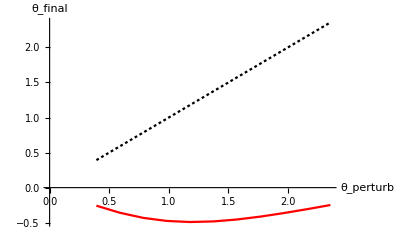

```mathematica
sp=0.5;
θpList = Pi*Range[1/8,6/8,1/16];
θfList = θfinal[#,sp]&/@θpList; (*this step will take a long time *)
muangleplot = ListLinePlot[{Transpose[{θpList,θpList}],Transpose[{θpList,θfList}]},PlotStyle->{{Dashing[Tiny],RGBColor[0,0,0]},RGBColor[1,0,0]},AxesLabel->{"θ_perturb","θ_final"}]
```

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

NDSolve::mxsst: Using maximum number of grid points 200 allowed by the MaxPoints or MinStepSize options for independent variable θ.

NDSolve::eerr: Warning: scaled local spatial error estimate of 79.3098 at t = 20. in the direction of independent variable θ is much greater than the prescribed error tolerance. Grid spacing with 201 points may be too large to achieve the desired accuracy or precision. A singularity may have formed or a smaller grid spacing can be specified using the MaxStepSize or MinPoints method options.

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

NDSolve::mxsst: Using maximum number of grid points 200 allowed by the MaxPoints or MinStepSize options for independent variable θ.

NDSolve::eerr: Warning: scaled local spatial error estimate of 73.9336 at t = 20. in the direction of independent variable θ is much greater than the prescribed error tolerance. Grid spacing with 201 points may be too large to achieve the desired accuracy or precision. A singularity may have formed or a smaller grid spacing can be specified using the MaxStepSize or MinPoints method options.

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

General::stop: Further output of NDSolve::pdord will be suppressed during this calculation.

NDSolve::mxsst: Using maximum number of grid points 200 allowed by the MaxPoints or MinStepSize options for independent variable θ.

General::stop: Further output of NDSolve::mxsst will be suppressed during this calculation.

NDSolve::eerr: Warning: scaled local spatial error estimate of 67.9 at t = 20. in the direction of independent variable θ is much greater than the prescribed error tolerance. Grid spacing with 201 points may be too large to achieve the desired accuracy or precision. A singularity may have formed or a smaller grid spacing can be specified using the MaxStepSize or MinPoints method options.

General::stop: Further output of NDSolve::eerr will be suppressed during this calculation.

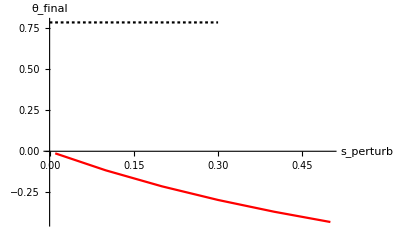

```mathematica
θp = Pi*1/4;
spList = {0.01,0.1,0.2,0.3, 0.4,0.5};
θfList = θfinal[θp,#]&/@spList; (*this step will take a long time *)
musplot = ListPlot[{Transpose[{{0,0.5},{θp,θp}}],Transpose[{spList,θfList}]},PlotStyle->{{Dashing[Tiny],RGBColor[0,0,0]},RGBColor[1,0,0]},Joined->True,AxesLabel->{"s_perturb","θ_final"}]
```